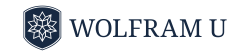

# Introduction to quantum computing

## Lesson 1: Classical Computation

## Overview

We begin with a brief revisit of classical computation through a series of hands-on examples. From there, the focus transitions to the quantum domain, where you will explore several examples of quantum circuits. Each example is accompanied by corresponding code; it’s perfectly fine if not everything is immediately clear. As you move forward, your grasp of quantum principles and your coding proficiency will develop together, reinforcing one another through practice and exploration.

## Addition: example 1

In order to understand quantum computation, it helps to compare it to classical computation. To compute something, you have to be able to use rules to determine what should be the output from a list of inputs. You can think of computing as starting with the inputs and following the rules to reach an output.

Consider two binary numbers “01” and “10” and let’s see how we can add them. First, each bit-string is interpreted as a base-2 number rather than ordinary decimal, so “01” becomes one and “10” becomes two.

Define binary strings:

```mathematica
a="01";b="10";
```

Construct the number from the base-2 digits of a:

```mathematica
FromDigits[a,2]
```

1

Construct the number from the base-2 digits of b:

```mathematica
FromDigits[b,2]
```

2

Add the numbers using normal addition:

```mathematica
FromDigits[a,2]+FromDigits[b,2]
```

3

Convert the total back into bit-string:

```mathematica
IntegerString[FromDigits[a,2]+FromDigits[b,2],2]
```

11

## Addition: example 2

To get a better sense of constructs of numbers in a base b, let’s consider symbolic digits and base:

```mathematica
Expand[FromDigits[{c4,c3,c2,c1,c0},b]]
```

c0+b c1+b^2 c2+b^3 c3+b^4 c4

Donating the length of digits by n, the maximum power of b will be b^(n-1) (in the above example, b^(5-1)).

Let’s consider another example. Add two binary strings 100 and 011:

```mathematica
a="101";
b="011";
IntegerString[FromDigits[a,2]+FromDigits[b,2],2]
```

1000

Note that something interesting happened in above calculation. Pay attention to the string length of initial numbers and final total. The original bit-strings had the string length of 3 while the final answer is a four-bit string. Let’s dive in a bit more.

What are all the states of a sequence of three classical bits?

```mathematica
threeBits=Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

What are the corresponding numbers from above base-2 digits?

```mathematica
FromDigits[#,2]&/@threeBits
```

{0,1,2,3,4,5,6,7}

## Addition: example 3

With a 3-bit string you can represent 0–7; in general, n bits represent 0 to 2^n-1. Returning to the example, adding 101 and 011 gives 8, which exceeds the 3-bit range. This means in-place addition is modulo 2^n, so the sum wraps to 000 unless you provide an extra bit to capture the carry.

```mathematica
FromDigits[a,2]+FromDigits[b,2]
```

8

To encode that result as a bitstring, we need at least 4 bits (since 8 requires 4-bit representation).

```mathematica
IntegerString[FromDigits[a,2]+FromDigits[b,2],2]
```

1000

If you insist on staying within 3 bits, perform all operations modulo 8 (wrap-around arithmetic).

```mathematica
Mod[FromDigits[a,2]+FromDigits[b,2],2^3]
```

0

Then the 3-bit string of the above result is:

```mathematica
IntegerString[0,2,3]
```

000

## Another encoding scheme

Now let’s try another encoding scheme.

It is also possible to encode information in such sequences of classical bits to represent problems of interest. For example, each of those bit sequences could also encode letter characters with a different encoding scheme:

```mathematica
AssociationMap[FromLetterNumber[FromDigits[#,2]]&,threeBits]
```

<|{0,0,0}→ ,{0,0,1}→a,{0,1,0}→b,{0,1,1}→c,{1,0,0}→d,{1,0,1}→e,{1,1,0}→f,{1,1,1}→g|>

With yet another encoding scheme, those same bit sequences could represent colors with opacity:

```mathematica
AssociationMap[Apply[RGBColor,#]&,threeBits]
```

<|{0,0,0}→RGBColor[0, 0, 0],{0,0,1}→RGBColor[0, 0, 1],{0,1,0}→RGBColor[0, 1, 0],{0,1,1}→RGBColor[0, 1, 1],{1,0,0}→RGBColor[1, 0, 0],{1,0,1}→RGBColor[1, 0, 1],{1,1,0}→RGBColor[1, 1, 0],{1,1,1}→RGBColor[1, 1, 1]|>

Having seen how a 3-bit register cleanly enumerates eight distinct states and how different encodings map those states to numbers, letters, or colors, we now move to the quantum setting. There the same eight basis strings exist, but a 3-qubit register can also occupy complex superpositions of them, and even entangled combinations that have no classical analogue. The rules for storing and extracting information therefore change: measurement reveals a single basis outcome, while computation exploits interference among amplitudes.

## Summary

Classical computation can be represented as some rules to determine what should be the output from a list of inputs.

With a 3-bit string you can represent 0–7; in general, n bits represent 0 to 2^n-1.